Dirac neutrinos in the singlet-doublet Dirac DM

```mathematica
Quit;
```

```mathematica
ClearAll["Global`*"];
$FeynArtsPath=SetDirectory["~/Work/FeynArts-3.9"]
<<FeynArts`
SetDirectory[$FeynArtsPath<>""]
$FormCalcPath=SetDirectory["~/Work/FormCalc-8.3"]
<<FormCalc`
SetDirectory[$FormCalcPath<>""]
```

/home/anferivera/Work/FeynArts-3.9

FeynArts 3.9 (8 Jul 2015)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

/home/anferivera/Work/FeynArts-3.9

/home/anferivera/Work/FormCalc-8.3

FormCalc 8.3

by Thomas Hahn

last revised 14 Nov 13

/home/anferivera/Work/FormCalc-8.3

Process:    S^0 ν_R ⟶ ϕ^0ν_L

Only one family

```mathematica
T2DM2S=CreateTopologies[1,2->2,ExcludeTopologies->{SelfEnergies,Tadpoles,Internal}];
```

> Top. 1: 1 diagram

> Top. 2: 1 diagram

> Top. 3: 1 diagram

> Top. 4: 1 diagram

> Top. 5: 1 diagram

> Top. 6: 1 diagram

> Top. 7: 1 diagram

> Top. 8: 1 diagram

> Top. 9: 1 diagram

> Top. 10: 1 diagram

> Top. 11: 1 diagram

> Top. 12: 1 diagram

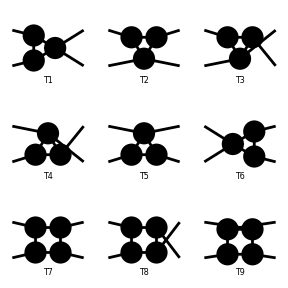

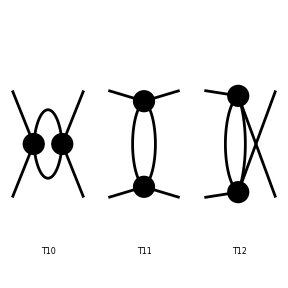

FeynArtsGraphics[2→2][([T1] | [T2] | [T3]
[T4] | [T5] | [T6]
[T7] | [T8] | [T9]),([T10] | [T11] | [T12]
Null | Null | Null
Null | Null | Null)]

```mathematica
Paint[T2DM2S]
```

> Top. 1: 1 diagram

> Top. 2: 1 diagram

> Top. 3: 1 diagram

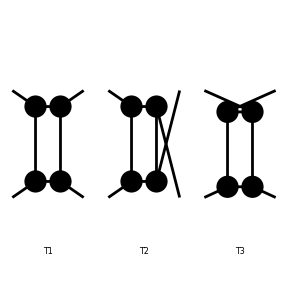

FeynArtsGraphics[2→2][([T1] | [T2] | [T3]
Null | Null | Null
Null | Null | Null)]

```mathematica
Paint[T2DM2S[[{7,8,9}]]]
```

Excluding 0 Generic, 4 Classes, and 8 Particles fields

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 0 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

> Top. 5: 11 Particles insertions

> Top. 6: 0 Particles insertions

> Top. 7: 62 Particles insertions

> Top. 8: 50 Particles insertions

> Top. 9: 62 Particles insertions

> Top. 10: 0 Particles insertions

> Top. 11: 0 Particles insertions

> Top. 12: 0 Particles insertions

Restoring 0 Generic, 4 Classes, and 8 Particles fields

in total: 185 Particles insertions

> Top. 1: 11 diagrams

> Top. 2: 62 diagrams

> Top. 3: 50 diagrams

> Top. 4: 62 diagrams

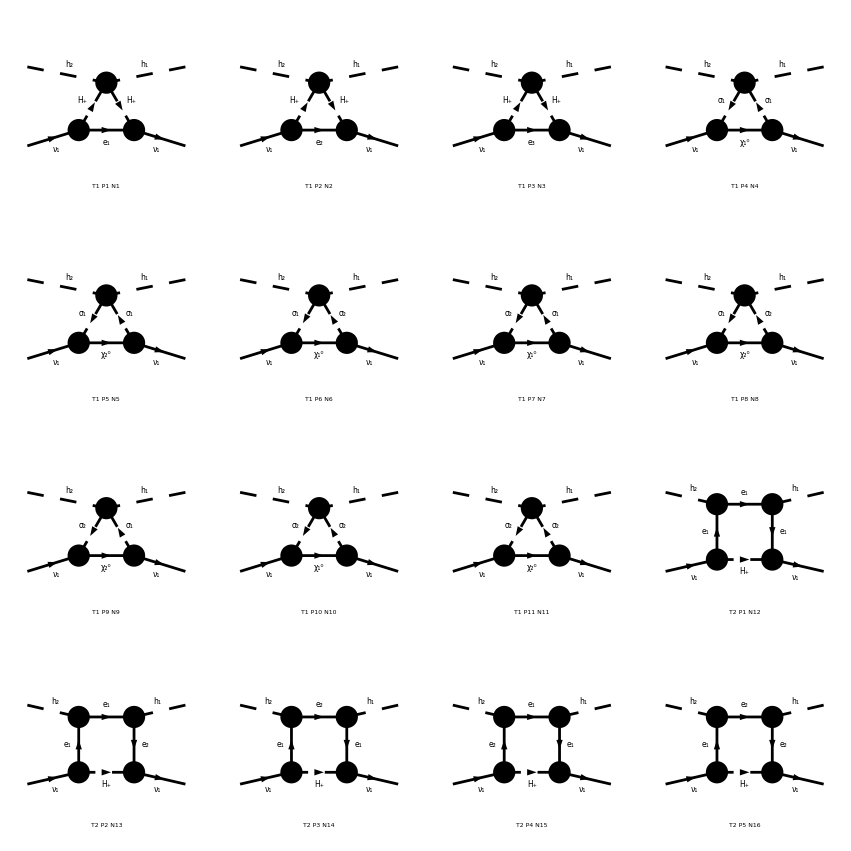

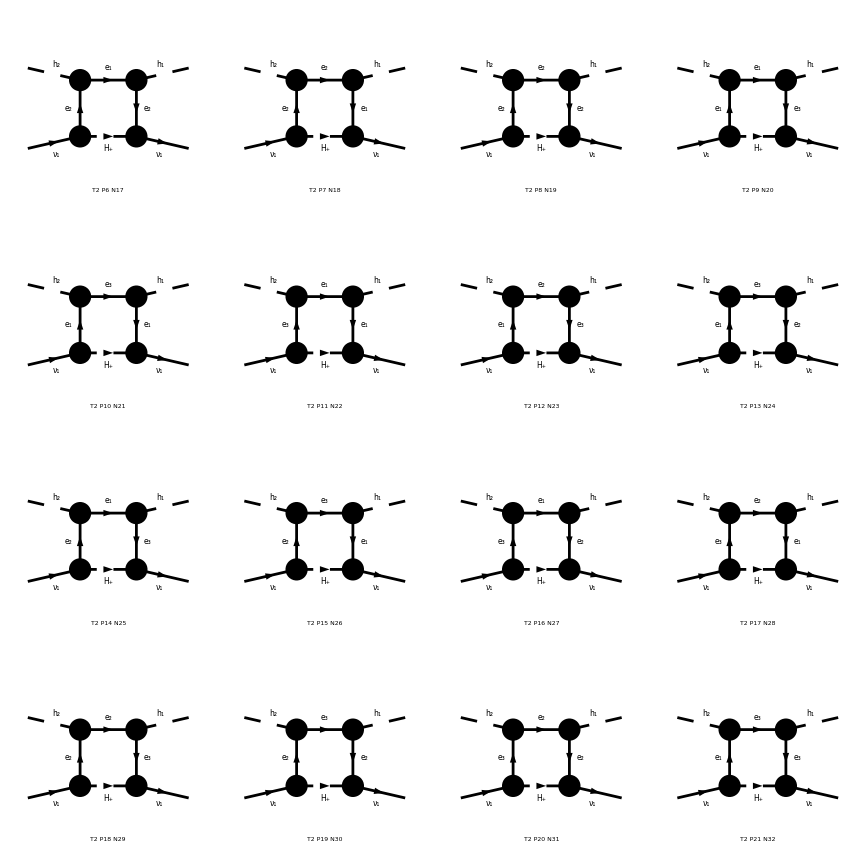

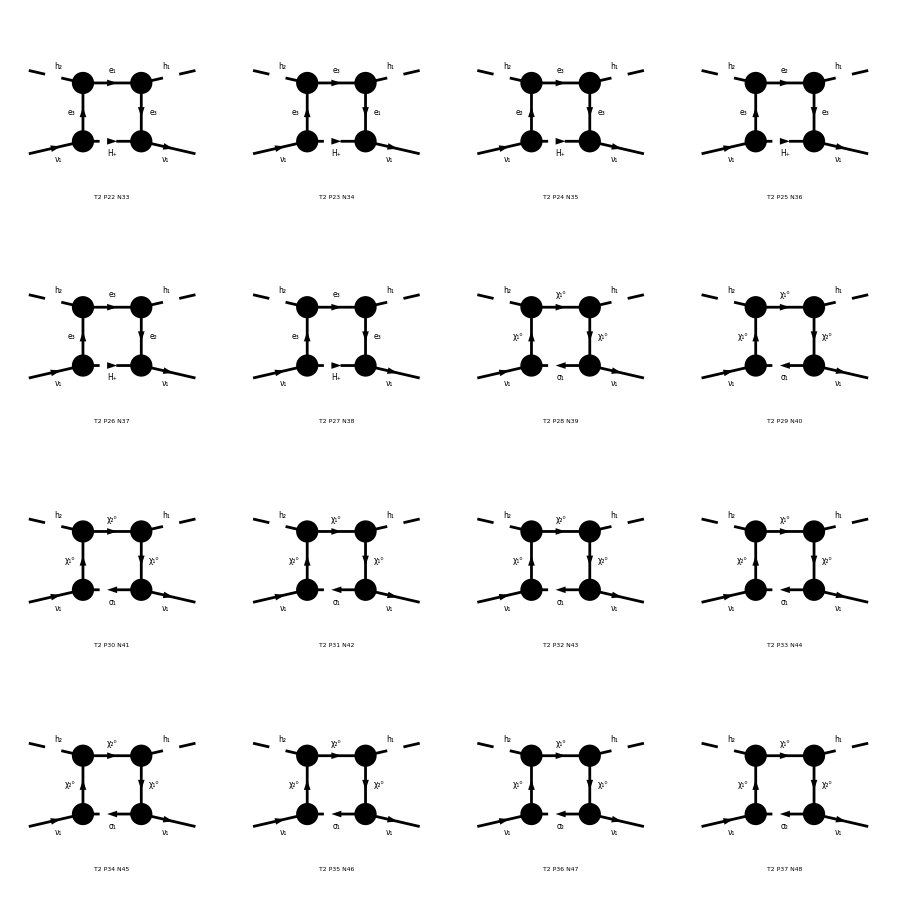

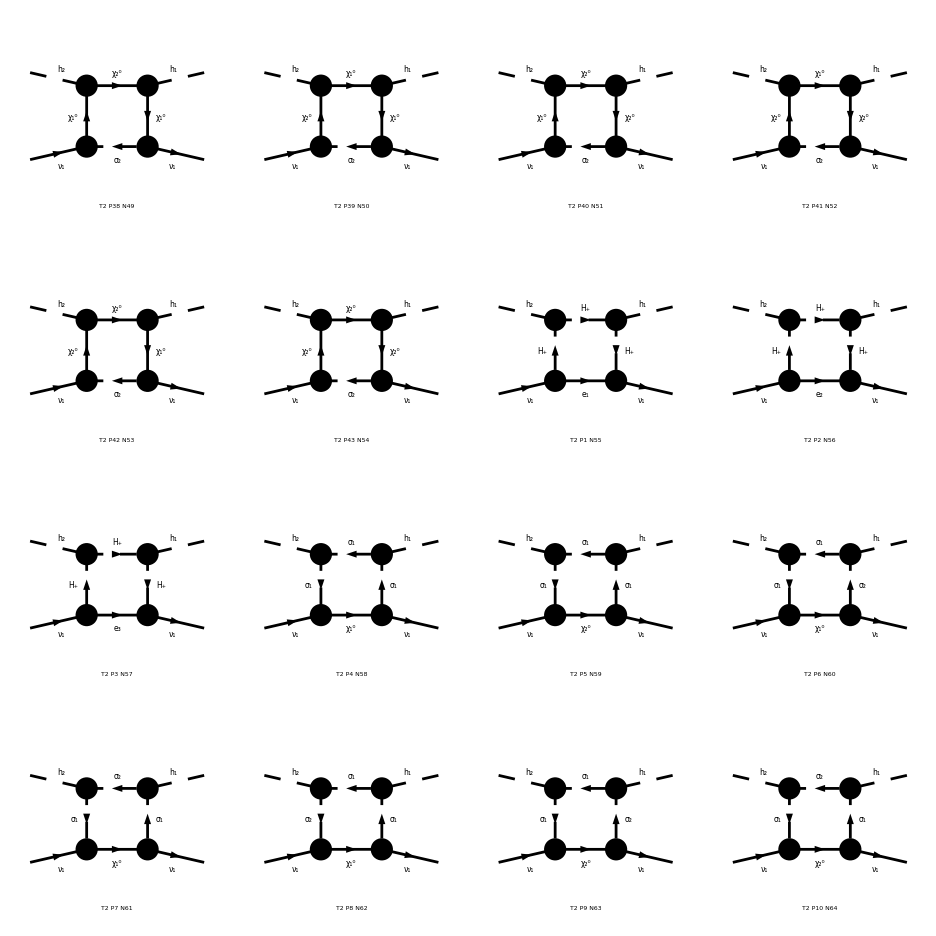

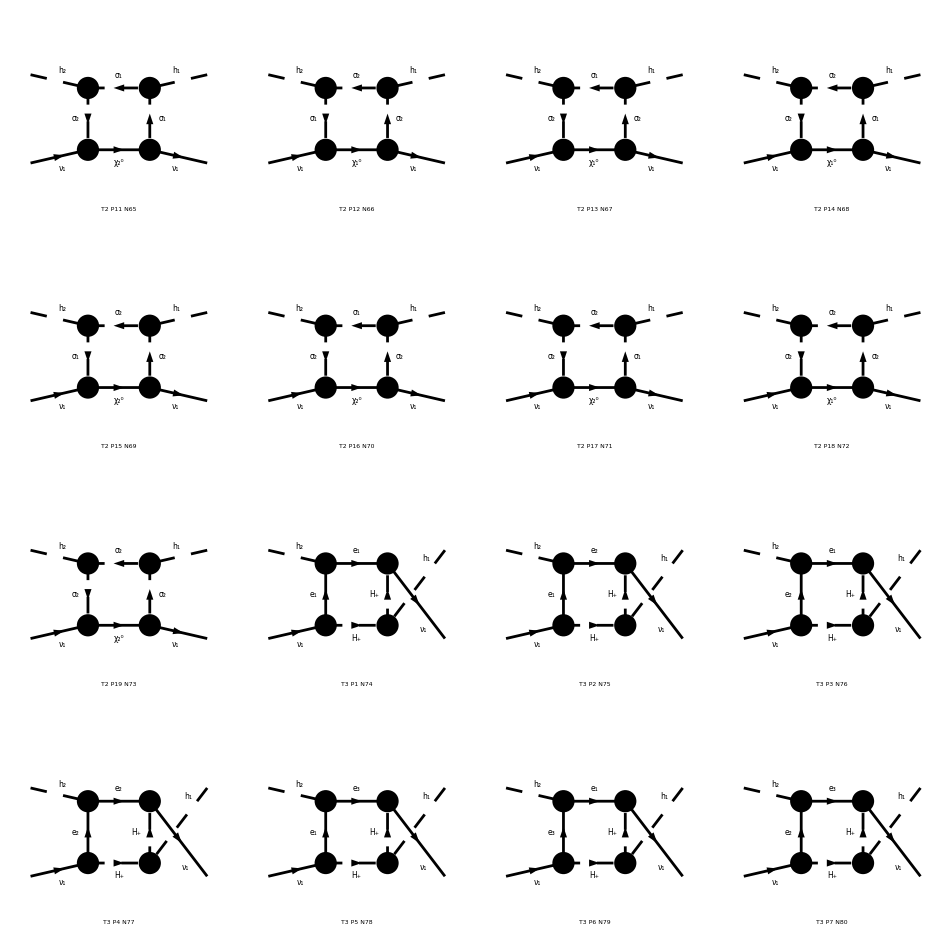

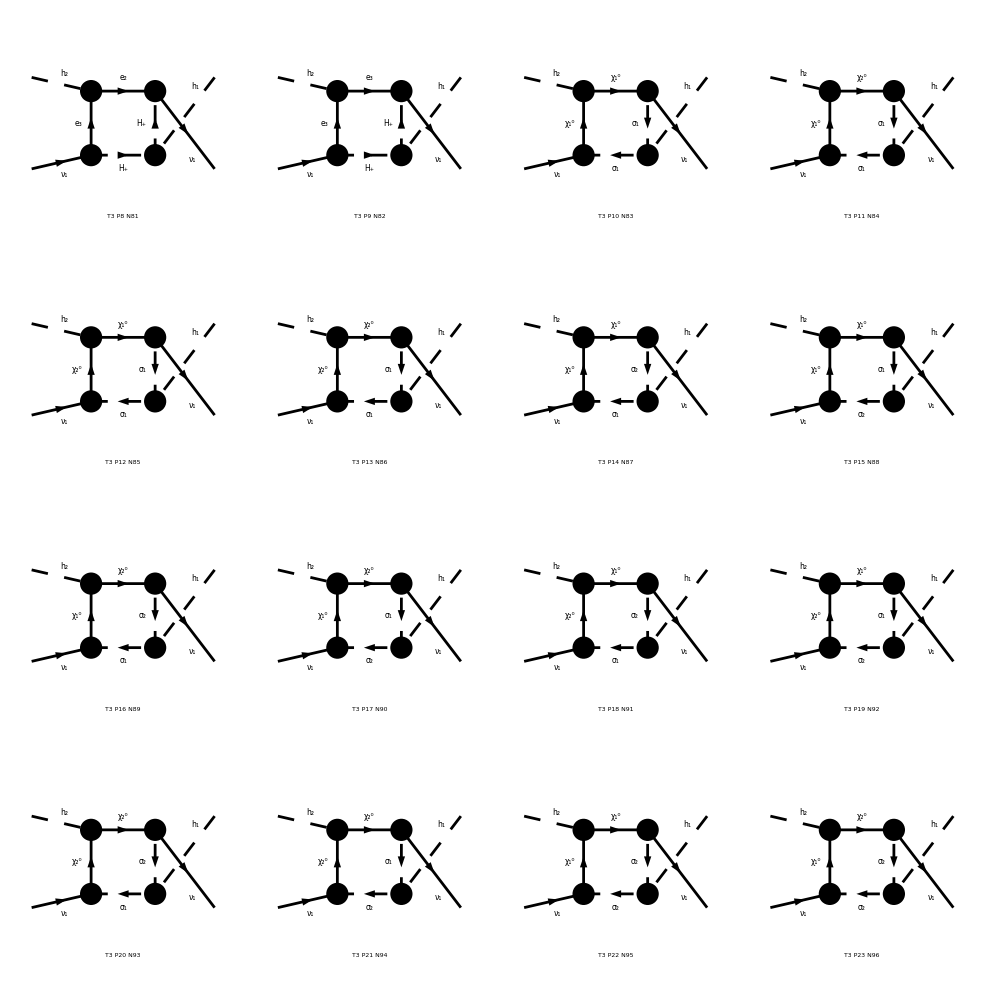

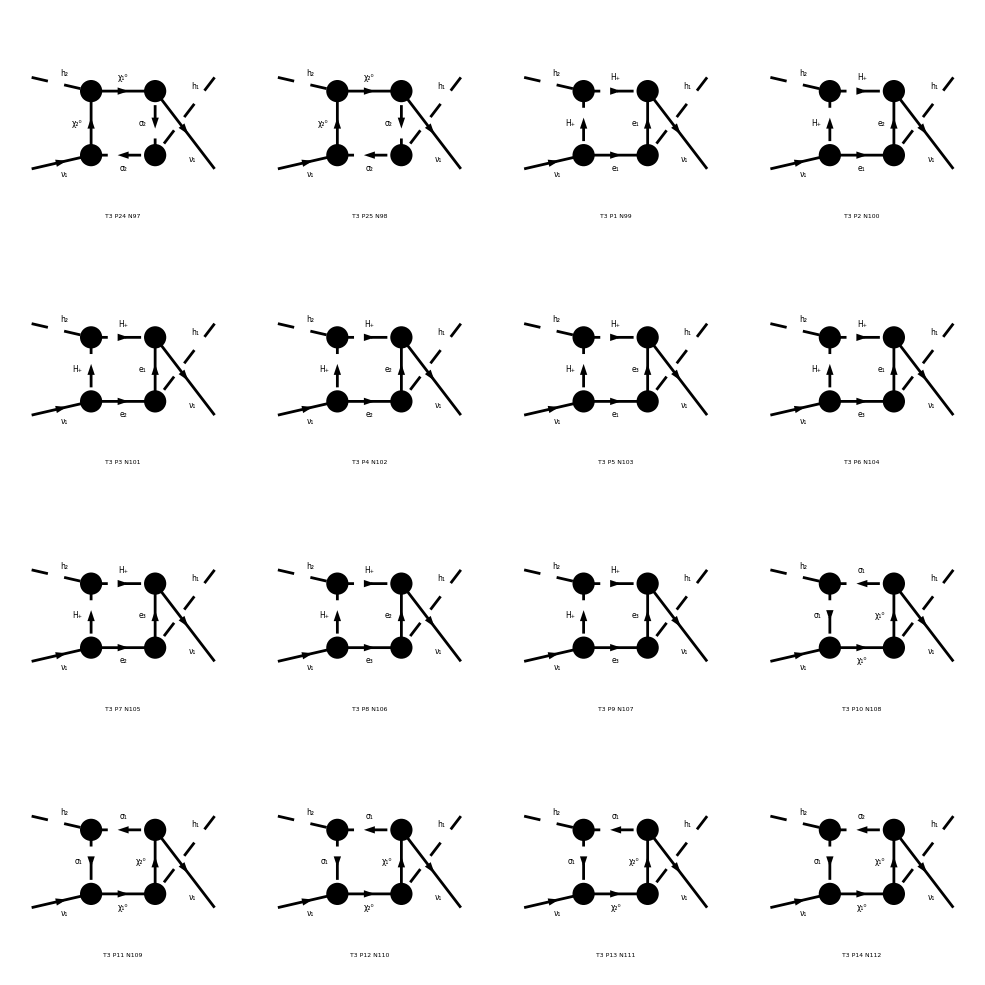

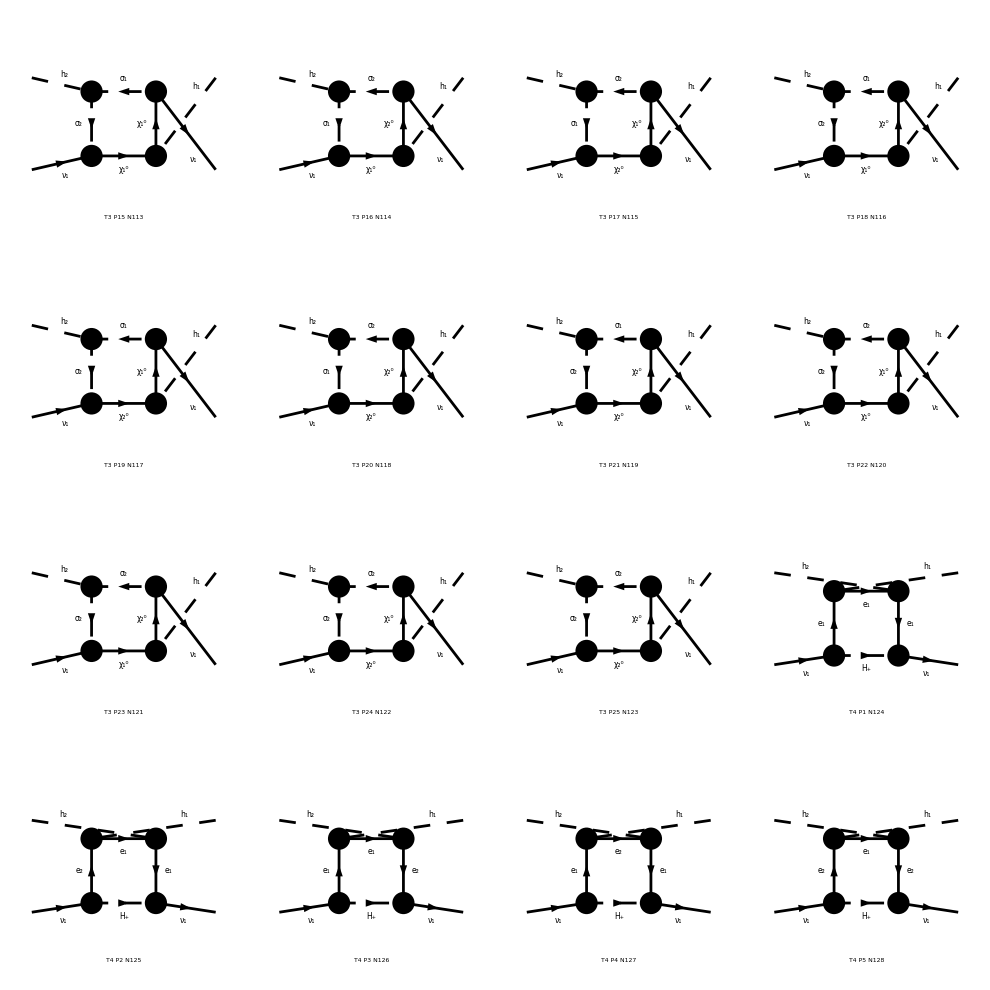

FeynArtsGraphics[{ComposedChar[h,2],ComposedChar[\nu,1]}→{ComposedChar[h,1],ComposedChar[\nu,1]}][([T1 P1 N1] | [T1 P2 N2] | [T1 P3 N3] | [T1 P4 N4]
[T1 P5 N5] | [T1 P6 N6] | [T1 P7 N7] | [T1 P8 N8]
[T1 P9 N9] | [T1 P10 N10] | [T1 P11 N11] | [T2 P1 N12]
[T2 P2 N13] | [T2 P3 N14] | [T2 P4 N15] | [T2 P5 N16]),([T2 P6 N17] | [T2 P7 N18] | [T2 P8 N19] | [T2 P9 N20]
[T2 P10 N21] | [T2 P11 N22] | [T2 P12 N23] | [T2 P13 N24]
[T2 P14 N25] | [T2 P15 N26] | [T2 P16 N27] | [T2 P17 N28]
[T2 P18 N29] | [T2 P19 N30] | [T2 P20 N31] | [T2 P21 N32]),([T2 P22 N33] | [T2 P23 N34] | [T2 P24 N35] | [T2 P25 N36]
[T2 P26 N37] | [T2 P27 N38] | [T2 P28 N39] | [T2 P29 N40]
[T2 P30 N41] | [T2 P31 N42] | [T2 P32 N43] | [T2 P33 N44]
[T2 P34 N45] | [T2 P35 N46] | [T2 P36 N47] | [T2 P37 N48]),([T2 P38 N49] | [T2 P39 N50] | [T2 P40 N51] | [T2 P41 N52]
[T2 P42 N53] | [T2 P43 N54] | [T2 P1 N55] | [T2 P2 N56]
[T2 P3 N57] | [T2 P4 N58] | [T2 P5 N59] | [T2 P6 N60]
[T2 P7 N61] | [T2 P8 N62] | [T2 P9 N63] | [T2 P10 N64]),([T2 P11 N65] | [T2 P12 N66] | [T2 P13 N67] | [T2 P14 N68]
[T2 P15 N69] | [T2 P16 N70] | [T2 P17 N71] | [T2 P18 N72]
[T2 P19 N73] | [T3 P1 N74] | [T3 P2 N75] | [T3 P3 N76]
[T3 P4 N77] | [T3 P5 N78] | [T3 P6 N79] | [T3 P7 N80]),([T3 P8 N81] | [T3 P9 N82] | [T3 P10 N83] | [T3 P11 N84]
[T3 P12 N85] | [T3 P13 N86] | [T3 P14 N87] | [T3 P15 N88]
[T3 P16 N89] | [T3 P17 N90] | [T3 P18 N91] | [T3 P19 N92]
[T3 P20 N93] | [T3 P21 N94] | [T3 P22 N95] | [T3 P23 N96]),([T3 P24 N97] | [T3 P25 N98] | [T3 P1 N99] | [T3 P2 N100]
[T3 P3 N101] | [T3 P4 N102] | [T3 P5 N103] | [T3 P6 N104]
[T3 P7 N105] | [T3 P8 N106] | [T3 P9 N107] | [T3 P10 N108]
[T3 P11 N109] | [T3 P12 N110] | [T3 P13 N111] | [T3 P14 N112]),([T3 P15 N113] | [T3 P16 N114] | [T3 P17 N115] | [T3 P18 N116]
[T3 P19 N117] | [T3 P20 N118] | [T3 P21 N119] | [T3 P22 N120]
[T3 P23 N121] | [T3 P24 N122] | [T3 P25 N123] | [T4 P1 N124]
[T4 P2 N125] | [T4 P3 N126] | [T4 P4 N127] | [T4 P5 N128]),([T4 P6 N129] | [T4 P7 N130] | [T4 P8 N131] | [T4 P9 N132]
[T4 P10 N133] | [T4 P11 N134] | [T4 P12 N135] | [T4 P13 N136]
[T4 P14 N137] | [T4 P15 N138] | [T4 P16 N139] | [T4 P17 N140]
[T4 P18 N141] | [T4 P19 N142] | [T4 P20 N143] | [T4 P21 N144]),([T4 P22 N145] | [T4 P23 N146] | [T4 P24 N147] | [T4 P25 N148]
[T4 P26 N149] | [T4 P27 N150] | [T4 P28 N151] | [T4 P29 N152]
[T4 P30 N153] | [T4 P31 N154] | [T4 P32 N155] | [T4 P33 N156]
[T4 P34 N157] | [T4 P35 N158] | [T4 P36 N159] | [T4 P37 N160]),([T4 P38 N161] | [T4 P39 N162] | [T4 P40 N163] | [T4 P41 N164]
[T4 P42 N165] | [T4 P43 N166] | [T4 P1 N167] | [T4 P2 N168]
[T4 P3 N169] | [T4 P4 N170] | [T4 P5 N171] | [T4 P6 N172]
[T4 P7 N173] | [T4 P8 N174] | [T4 P9 N175] | [T4 P10 N176]),([T4 P11 N177] | [T4 P12 N178] | [T4 P13 N179] | [T4 P14 N180]
[T4 P15 N181] | [T4 P16 N182] | [T4 P17 N183] | [T4 P18 N184]
[T4 P19 N185] | Null | Null | Null
Null | Null | Null | Null)]

```mathematica
n22=InsertFields[T2DM2S,{S[1,{2}],F[1,{1}]}->{S[1,{1}],F[1,{1}]},InsertionLevel->{Particles},Model->"SDdiracDMEWSB",GenericModel->"Lorentz",ExcludeParticles->{F[1,{2}],F[1,{3}],V[2],V[3],S[2]}];
Paint[n22,ColumnsXRows->4]
```

Amplitude in process..

```mathematica
CreateFeynAmp[n22]
```

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

in total: 1 Particles amplitude

FeynAmpList[Process→{{S[1],p1,Masshh,{}},{S[1],p2,Masshh,{}}}→{{S[1],k1,Masshh,{}},{S[1],k2,Masshh,{}}},Model→{SDdiracDMEWSB},GenericModel→{Lorentz},AmplitudeLevel→{Particles},ExcludeParticles→{-F[6,{2}],F[6,{2}]},ExcludeFieldPoints→{},LastSelections→{}][FeynAmp[GraphID[Topology==1,Generic==1,Particles==1,Number==1],Integral[],-3 Lam]]

```mathematica
resultn22=CalcFeynAmp[CreateFeynAmp[n22],FermionChains->VA,Antisymmetrize->False,Invariants->True];
```

creating amplitudes at level(s) {Particles}

> Top. 1: 16 Particles amplitudes

> Top. 2: 16 Particles amplitudes

in total: 32 Particles amplitudes

preparing FORM code in /home/anferivera/Work/FormCalc-8.3/fc-amp-14.frm

running FORM...

```mathematica
resultn22
```

resultn22

Simplifications

```mathematica
Den[x_,y_]:=1/(x-y)

expr1=Simplify[ComplexExpand[ Plus@@resultn22//.Subexpr[]//.Abbr[] //.{MassVWp->mw,MassVZ->mz,MassHp->mw,MassAh->mz, MassFe[3]->mta,MassFu[3]->mt,MassFd[3]->mb,Yu[3,3]->yt,Yd[3,3]->yb,Ye[3,3]->yta,Masshh[1]->ms1,Masshh[2]->ms2,ZH[1,1]->ZH11,ZH[1,2]->ZH12,ZH[2,1]->ZH21,ZH[2,2]->ZH22,ZX[1,1]->ZX11,ZX[1,2]->ZX12,ZX[2,1]->ZX21,ZX[2,2]->ZX22,ZX21->ZX12,ZH21->-ZH12(*,ZDL[1,1]->1,ZDL[1,2]->0,ZDL[1,3]->0,ZDR[1,1]->1,ZDR[1,2]->0,ZDR[1,3]->0*)}
]]
```

1/(4 √2 (ms1^2-T) (-ms2^2+T))YTS ZH12 (-ms2^2 ZH11+T (ZH11-ZH22)+ms1^2 ZH22) ZX11 ZX12 (2 Mat[(<v1|1|u2>) (<u3|1|v4>) SUNT[Col1,Col3]]-2 Mat[(<v1|5|u2>) (<u3|5|v4>) SUNT[Col1,Col3]]+2 Mat[(<v1|1,Lor[1]|u2>) (<u3|1,Lor[1]|v4>) SUNT[Col1,Col3]]+2 Mat[(<v1|5,Lor[1]|u2>) (<u3|5,Lor[1]|v4>) SUNT[Col1,Col3]]-Mat[(<v1|1,Lor[1],Lor[2]|u2>) (<u3|1,Lor[1],Lor[2]|v4>) SUNT[Col1,Col3]]) Yd[1,1]

Simplify: ZUL the mixing for the lef up quaks and so on... No mixing imply:

```mathematica
ZUL[a_,b_]:=KroneckerDelta[a,b];
ZUR[a_,b_]:=KroneckerDelta[a,b];
ZDL[a_,b_]:=KroneckerDelta[a,b];
ZDR[a_,b_]:=KroneckerDelta[a,b];
ZEL[a_,b_]:=KroneckerDelta[a,b];
ZER[a_,b_]:=KroneckerDelta[a,b];
```

```mathematica
expr1
```

-1/(4 √2 (ms1^2-T) (-ms2^2+T))YTS (ms2^2 ZH11 ZH12+ms1^2 ZH1 ZH22-T (ZH11 ZH12+ZH1 ZH22)) ZX11 ZX12 (2 Mat[(<v1|1|u2>) (<u3|1|v4>) SUNT[Col1,Col3]]-2 Mat[(<v1|5|u2>) (<u3|5|v4>) SUNT[Col1,Col3]]+2 Mat[(<v1|1,Lor[1]|u2>) (<u3|1,Lor[1]|v4>) SUNT[Col1,Col3]]+2 Mat[(<v1|5,Lor[1]|u2>) (<u3|5,Lor[1]|v4>) SUNT[Col1,Col3]]-Mat[(<v1|1,Lor[1],Lor[2]|u2>) (<u3|1,Lor[1],Lor[2]|v4>) SUNT[Col1,Col3]]) Yd[1,1]

#### Final Dirac Chains after de Pairs reduction

```mathematica
expr1//.{
(*,

Mat[DiracChain[Spinor[k[1],m,-1],1,Spinor[k[1],m,1]]]->0,(*cero*)
Mat[DiracChain[Spinor[k[1],m,-1],1,k[3],Spinor[k[1],m,1]]]->0,(*cero*)
Mat[DiracChain[Spinor[k[1],m,-1],1,ec[3],ec[4],k[3],Spinor[k[1],m,1]]]->FA04,
Mat[DiracChain[Spinor[k[1],m,-1],1,ec[3],ec[4],Spinor[k[1],m,1]]]->0,(*cero*)

Mat[DiracChain[Spinor[k[1],m,-1],5,Spinor[k[1],m,1]]]->FA01,
Mat[DiracChain[Spinor[k[1],m,-1],5,k[3],Spinor[k[1],m,1]]]->FA02,
Mat[DiracChain[Spinor[k[1],m,-1],5,Lor[1],Spinor[k[1],m,1]]*Eps[Lor[1],ec[3],ec[4],k[1]]]->FA05,
Mat[DiracChain[Spinor[k[1],m,-1],5,Lor[1],Spinor[k[1],m,1]]*Eps[Lor[1],ec[3],ec[4],k[3]]]->FA07,
Mat[DiracChain[Spinor[k[1],m,-1],5,Lor[1],Spinor[k[1],m,1]]*Eps[Lor[1],ec[3],ec[4],k[4]]]->FA08*)
}
```

-1/(4 √2 (ms1^2-T) (-ms2^2+T))YTS ZH12 (ms2^2 ZH11+ms1^2 ZH22-T (ZH11+ZH22)) ZX11 ZX12 (2 Mat[(<v1|1|u2>) (<u3|1|v4>) SUNT[Col1,Col3]]-2 Mat[(<v1|5|u2>) (<u3|5|v4>) SUNT[Col1,Col3]]+2 Mat[(<v1|1,Lor[1]|u2>) (<u3|1,Lor[1]|v4>) SUNT[Col1,Col3]]+2 Mat[(<v1|5,Lor[1]|u2>) (<u3|5,Lor[1]|v4>) SUNT[Col1,Col3]]-Mat[(<v1|1,Lor[1],Lor[2]|u2>) (<u3|1,Lor[1],Lor[2]|v4>) SUNT[Col1,Col3]]) Yd[1,1]

```mathematica
Aproximation
```

```mathematica
expr2=Simplify[expr1//.{ZH11->ZH22}]
```

1/(4 √2 (ms1^2-T) (-ms2^2+T))(ms1^2-ms2^2) YTS ZH12 ZH22 ZX11 ZX12 (2 Mat[(<v1|1|u2>) (<u3|1|v4>) SUNT[Col1,Col3]]-2 Mat[(<v1|5|u2>) (<u3|5|v4>) SUNT[Col1,Col3]]+2 Mat[(<v1|1,Lor[1]|u2>) (<u3|1,Lor[1]|v4>) SUNT[Col1,Col3]]+2 Mat[(<v1|5,Lor[1]|u2>) (<u3|5,Lor[1]|v4>) SUNT[Col1,Col3]]-Mat[(<v1|1,Lor[1],Lor[2]|u2>) (<u3|1,Lor[1],Lor[2]|v4>) SUNT[Col1,Col3]]) Yd[1,1]